## Creating some mock data

```mathematica
SeedRandom[3523] (*Sets a fixed seed for reproducibility*)
means={{10,20},{30,50},{60,70}};
kk = 3; (*Number of clusters*)
dd= 2; (*Assume two features like weight and height*)
nums = {150,90,200};
stds = {5,8,6};
rN[m_,s_]:=Random[NormalDistribution[m,s]]
makePoint[mean_,std_]:={rN[mean[[1]],std],rN[mean[[2]],std]}
```

```mathematica
makePoint[{100,100},10]
```

{109.978,109.125}

```mathematica
(*I did "divide cell" in the cell menu to break up the cell*)
```

```mathematica
vec={1,2,3,4,-4,12}
vec[[5]] (* [[ ]] get the 5'th index*)
```

{1,2,3,4,-4,12}

-4

```mathematica
pts = Table[
Table[makePoint[means[[k]],stds[[k]]],nums[[k]]],
{k,1,kk}];
```

```mathematica
Length[pts]
```

3

```mathematica
Length[pts[[2]]]
```

90

```mathematica
Length /@ pts  (*Maps the Length function to pts*)
```

{150,90,200}

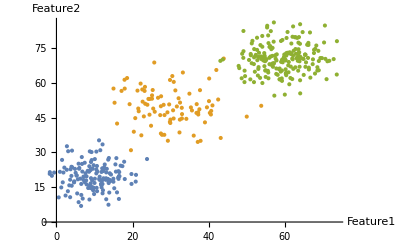

```mathematica
ListPlot[pts,AxesLabel->{"Feature1","Feature2"}]
```

```mathematica
data = Flatten[Join[pts],1]; (*Make it one big group*)
```

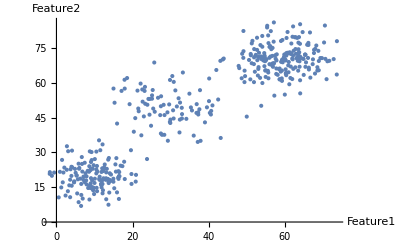

```mathematica
ListPlot[data,AxesLabel->{"Feature1","Feature2"}]
```

## The k-means algorithm

```mathematica
nn=Length[data]
```

440

```mathematica
dd = Length[data[[1]]]
```

2

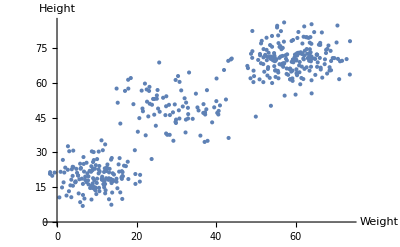

```mathematica
ListPlot[data,AxesLabel->{"Weight","Height"}]
```

Let us assume 3 clusters

```mathematica
SeedRandom[0]
```

```mathematica
kk=5
```

5

```mathematica
minV = Min[data]
maxV = Max[data]
```

-1.76297

86.0416

```mathematica
rP:=RandomReal[{minV,maxV}]
```

```mathematica
rP
```

75.2143

```mathematica
centroids = {{rP,rP},{rP,rP},{rP,rP},{rP,rP},{rP,rP}}
```

{{28.1153,23.0347},{24.2691,59.3448},{43.3776,66.8241},{33.6746,32.0552},{31.5847,36.2312}}

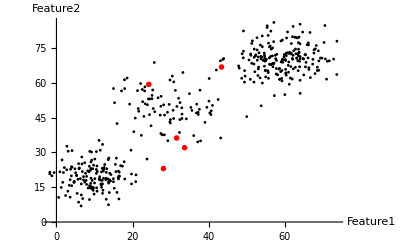

```mathematica
ListPlot[{data,centroids},AxesLabel->{"Feature1","Feature2"},PlotStyle->{{PointSize[0.005],Black},{PointSize[0.01],Red}}]
```

```mathematica
?Norm
```

```mathematica
distsToCentroids[i_]:=Table[Norm[data[[i]] -centroids[[k]]],{k,1,kk}]
```

```mathematica
distsToCentroids[440] (*The three distances between the 440'th point and the centroids*)
```

{58.4311,38.1928,17.7127,47.8421,45.7265}

```mathematica
currentCluster[i_]:=Ordering[distsToCentroids[i]][[1]] (*choose the closest index*)
```

```mathematica
currentCluster[440]
```

1

```mathematica
clusterMapping = Table[currentCluster[i], {i, 1, nn}] ;
```

```mathematica
clusterMapping
```

{3,2,3,2,3,3,2,2,3,2,3,3,3,3,2,3,2,3,3,2,2,3,3,2,3,3,2,3,2,3,2,3,3,2,2,3,3,3,2,2,2,3,3,3,3,3,3,2,3,3,3,3,3,2,3,2,3,2,2,2,2,3,2,2,2,2,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,2,3,2,3,2,3,2,2,2,3,3,3,2,3,3,3,2,2,2,3,3,3,3,3,3,2,3,2,3,3,2,2,3,3,3,3,3,3,2,2,2,2,3,2,3,2,3,2,3,3,2,2,3,3,2,3,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Look for help of Pick[]*)
mappedPoints = Table[
Pick[data,clusterMapping,k],{k,1,kk}];
```

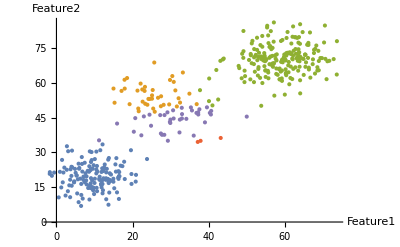

```mathematica
ListPlot[mappedPoints,AxesLabel->{"Feature1","Feature2"}]
```

```mathematica
Length[mappedPoints]
```

3

```mathematica
Length /@ mappedPoints
```

{189,161,90}

```mathematica
(*START SECOND iteration....*) (*Use Mean[] for centroids*)
centroids=Table[Mean[mappedPoints[[k]]],{k,1,kk}]
```

{{60.0534,70.8081},{25.4466,39.3887},{6.44936,19.9484}}

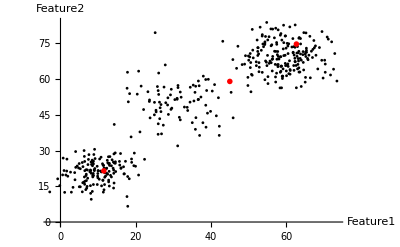

```mathematica
ListPlot[{data,centroids},AxesLabel->{"Feature1","Feature2"},PlotStyle->{{PointSize[0.005],Black},{PointSize[0.01],Red}}]
```

```mathematica
clusterMapping = Table[currentCluster[i], {i, 1, nn}] ;
```

```mathematica
mappedPoints = Table[
Pick[data,clusterMapping,k],{k,1,kk}];
```

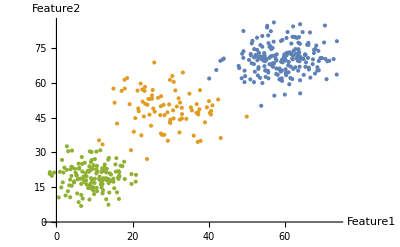

```mathematica
ListPlot[mappedPoints,AxesLabel->{"Feature1","Feature2"}]
```

```mathematica
? For
```

```mathematica
centroids = {{rP,rP},{rP,rP},{rP,rP},{rP,rP},{rP,rP}};
For[j=1,j≤ 10,j++,
clusterMapping = Table[currentCluster[i], {i, 1, nn}] ;
mappedPoints = Table[
Pick[data,clusterMapping,k],{k,1,kk}];
centroids=Table[Mean[mappedPoints[[k]]],{k,1,kk}];
Print[Length/@mappedPoints]
]
```

{191,42,207,0,0}

{193,80,167,0,0}

{201,88,151,0,0}

{203,86,151,0,0}

{203,86,151,0,0}

{203,86,151,0,0}

«4 more identical outputs»

```mathematica
ListPlot[mappedPoints,AxesLabel->{"Feature1","Feature2"}]
```

ListPlot::lpn: {{{42.0118,65.542},{43.9579,70.4753},«48»,«153»},{«1»,«49»,«36»},{«1»},{},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{{42.0118,65.542},{43.9579,70.4753},{53.8089,50.1068},{56.7809,68.1747},{69.7657,70.6617},{62.3275,73.8213},{59.004,78.0477},{56.7891,75.0666},{59.2027,61.9134},{65.3165,72.1794},{64.6899,81.8812},{68.2848,76.0932},{52.7062,79.4434},{68.0151,74.6456},{55.7058,61.9617},{56.748,71.6242},{50.6027,69.868},{59.4046,70.1393},{62.2026,71.8216},{65.4275,66.9067},{61.7109,72.735},{53.0457,65.9918},{60.2189,65.8335},{43.0732,69.476},{55.3554,83.8687},{61.963,70.4933},{54.0825,80.2174},{69.3602,70.6867},{63.4788,72.4418},{61.9575,61.6351},{48.6728,61.9693},{58.9275,64.8471},{71.6993,69.5032},{61.4791,62.0865},{54.3284,69.7027},{64.944,70.3079},{51.0854,71.8669},{66.2145,76.34},{60.9046,67.5224},{55.981,75.4759},{63.9906,76.8272},{73.7026,77.9588},{49.1508,73.6403},{53.5998,76.2851},{52.1368,64.7949},{67.9424,64.0061},{61.0528,68.9931},{62.2387,66.0192},{57.1656,68.4935},{66.7212,62.2482},{51.9577,74.5583},{53.1098,66.781},{48.8037,72.5303},{49.1012,70.7755},{68.948,69.4163},{61.2852,73.1725},{54.6535,71.8419},{65.8817,76.4417},{56.1731,75.8571},{65.3833,72.1995},{60.7084,72.9694},{59.3748,78.4777},{67.4032,70.1294},{61.7272,76.9516},{63.6698,73.0231},{70.545,84.7136},{63.2773,79.379},{51.047,72.4422},{57.597,70.4034},{55.0118,69.6335},{54.1137,59.9198},{51.9032,60.3087},{56.8025,68.3562},{60.0103,54.9318},{59.3726,69.8633},{63.6049,74.4887},{49.568,62.8964},{63.7388,79.7204},{59.2635,60.8427},{62.6504,79.6819},{53.9265,71.1279},{57.5011,71.8768},{60.3756,63.2974},{64.0239,61.1098},{52.3928,72.0696},{53.2297,72.9469},{62.1878,84.3178},{67.6919,74.2359},{66.1075,70.7366},{55.5632,65.1765},{60.987,64.5597},{58.1315,63.451},{64.0528,55.4604},{63.894,66.9401},{73.662,63.5825},{59.454,68.8557},{72.8473,70.2366},{57.8962,72.2866},{47.8772,67.2977},{55.3868,84.6092},{55.9788,68.0439},{57.077,77.7546},{58.4485,65.9528},{63.1201,70.6677},{55.9454,70.785},{71.1995,69.2973},{57.7871,66.1929},{63.8722,69.2867},{52.3038,71.5848},{56.3548,67.8449},{64.0314,71.3317},{61.6552,72.4337},{63.5937,71.6672},{60.2957,64.3013},{58.6364,66.1804},{56.3312,82.2953},{49.1358,82.3572},{59.8664,72.1872},{52.7211,74.2021},{50.9482,61.4992},{70.6755,70.3284},{54.6066,72.8305},{67.6672,72.8508},{56.4574,74.5194},{56.2684,71.3505},{68.5643,66.7322},{70.3243,77.3984},{54.0969,75.5553},{51.932,70.993},{64.0091,70.3896},{53.0471,71.1469},{48.0352,66.3522},{59.3201,69.8559},{63.4209,69.5111},{59.2533,65.312},{54.715,71.3499},{62.8222,74.5712},{57.2576,54.4875},{54.9683,65.4234},{55.7213,77.1217},{63.5244,65.2561},{60.1541,70.0146},{62.0873,70.1437},{60.3751,72.7556},{63.7938,73.1757},{43.7224,70.0849},{53.7037,71.3784},{55.6557,64.4496},{60.2219,69.6462},{49.4084,60.3209},{53.7784,70.3166},{64.0311,85.2726},{64.7805,70.4989},{61.5819,67.0015},{53.5097,62.1522},{66.6222,81.7205},{59.7905,71.1217},{65.4431,72.0568},{58.6426,61.4837},{62.0333,79.8695},{54.8621,65.2979},{60.2788,63.9535},{49.4385,65.2568},{55.6344,80.4371},{67.331,68.0648},{68.5529,65.3018},{57.1326,86.0416},{57.7557,63.8415},{62.8429,79.6583},{60.7265,81.9226},{57.0223,68.1911},{52.7831,69.7604},{63.1526,70.6402},{54.9782,62.558},{54.6984,69.6266},{51.3058,68.4485},{63.5843,77.3164},{59.0433,69.0434},{61.1908,59.39},{51.3273,77.0026},{60.4673,79.3426},{58.6546,61.5538},{66.3236,66.5488},{54.7413,70.5136},{54.7975,69.3349},{66.3384,65.7577},{54.6468,67.1844},{66.2031,77.2272},{64.978,63.422},{56.8854,66.9192},{68.9332,65.4303},{61.0705,72.7097},{52.9314,63.1664},{57.8234,69.6636},{51.8839,68.0886},{65.5802,68.8282},{62.9494,72.5157},{55.1664,70.1636},{70.9793,61.5803},{51.5012,78.1041},{62.7872,66.7007},{68.8224,73.7911},{60.3943,71.7405}},{{27.7462,37.6006},{23.1613,56.5152},{27.4405,49.9065},{39.0232,42.9605},{37.2691,46.3536},{40.6682,47.9042},{21.497,48.9287},{35.3294,49.4052},{25.2914,56.9066},{24.1697,53.066},{18.5629,62.0735},{32.9981,46.5186},{40.3059,47.0476},{22.3075,37.3745},{33.2175,64.4558},{15.2696,51.4285},{34.9392,55.3343},{32.3319,38.613},{29.8361,61.2442},{37.1327,34.5256},{37.2342,47.2864},{20.3311,38.929},{22.6466,51.8854},{25.1093,53.161},{32.478,51.4943},{31.6378,49.8149},{30.6504,48.1601},{28.3976,46.1029},{30.8234,60.4096},{32.9314,49.2351},{29.2787,35.0344},{21.6156,47.7476},{29.9471,44.1594},{23.3209,50.9863},{26.6888,53.5648},{19.2213,50.805},{28.1656,50.5266},{30.4462,62.9286},{32.429,44.1467},{17.1035,56.5239},{37.7192,56.8427},{29.6225,50.7013},{32.0956,53.3509},{32.9703,44.6387},{22.9649,45.5289},{37.8736,34.9994},{20.7091,44.7884},{15.93,42.4463},{24.4553,46.2744},{36.7956,47.03},{25.7048,68.7636},{27.2698,46.0858},{40.0828,52.112},{14.9889,57.5371},{36.0706,37.2525},{40.1316,61.8708},{22.115,59.6805},{29.8071,43.1608},{24.5237,53.0567},{37.5622,48.6042},{34.1337,44.4807},{39.5446,49.4429},{27.4968,54.2078},{43.1645,36.239},{30.7917,44.6244},{40.5884,46.352},{35.6078,48.1025},{25.1194,54.5896},{24.8594,41.5028},{22.5586,57.1482},{31.2468,56.7428},{50.0086,45.4423},{42.496,52.8182},{21.2929,56.6549},{36.8528,50.8213},{23.8912,50.5549},{17.9391,57.5234},{25.8271,47.5455},{29.9188,42.6908},{25.4255,48.9138},{27.4435,38.1641},{40.9924,50.2757},{17.8925,61.3271},{29.1669,47.2819},{23.2574,58.261},{28.3452,37.5939}},{{1.26535,14.9017},{16.316,18.5976},{9.38461,14.2962},{12.5435,23.5131},{2.0726,23.4588},{5.93307,22.9843},{14.9661,17.3612},{19.7118,20.6904},{5.04136,21.2258},{12.222,13.6983},{9.62892,14.9063},{7.79637,17.9299},{7.10243,19.5623},{9.71428,14.6723},{13.7265,16.7923},{9.53772,22.9635},{12.1156,12.3684},{6.26525,18.6962},{3.59781,10.6985},{15.4939,24.8493},{11.8496,16.3311},{3.93132,19.8827},{4.61786,17.1206},{11.2394,18.629},{-1.76297,20.757},{9.37698,17.9167},{20.8295,17.42},{6.79847,21.7577},{13.8762,12.698},{7.43149,25.5491},{12.9613,18.1854},{10.5569,14.7414},{5.29744,20.0192},{15.6281,21.726},{13.543,18.5651},{5.45013,12.3269},{7.10018,18.1333},{6.51887,16.4182},{15.9114,12.7755},{11.3126,18.2145},{14.957,18.6771},{9.03703,23.0794},{8.98884,16.637},{6.65971,28.0078},{5.62607,18.426},{10.4734,20.9665},{7.93097,16.203},{14.1938,17.6848},{10.0853,27.1324},{11.523,30.9556},{6.89781,10.103},{7.90724,19.6663},{10.6698,13.2883},{17.791,25.9932},{10.488,30.361},{12.1137,33.4615},{4.68233,17.535},{16.4944,21.5029},{16.4146,9.94528},{19.727,16.427},{11.7058,16.3198},{7.43391,17.1653},{16.2988,21.9225},{23.7992,27.1541},{15.1896,14.5586},{16.4305,19.8058},{13.6013,26.8944},{4.61442,17.2029},{-0.610256,21.3143},{-1.19997,19.9302},{4.09369,23.649},{-1.73278,21.4919},{9.75689,24.4985},{12.0107,17.9132},{8.694,15.6621},{10.4777,22.6545},{10.0909,18.6779},{9.26495,26.7059},{6.71177,25.0416},{3.37165,15.815},{9.21528,30.1592},{5.81751,25.1364},{9.12538,15.2784},{2.39192,11.4208},{12.1003,16.4075},{2.74803,32.6688},{8.56169,21.6688},{9.0662,25.8763},{6.53219,11.6699},{12.3274,21.9854},{0.595827,10.6104},{13.081,9.81374},{9.88916,12.0454},{11.8081,16.0339},{3.71262,22.7385},{11.3597,19.5423},{11.8373,21.5876},{11.5471,18.1465},{3.60067,18.2469},{4.86194,22.9255},{10.7436,21.7705},{16.2063,19.1805},{10.6381,24.1538},{8.3377,14.6671},{11.1908,35.2175},{14.3265,20.4656},{20.9045,20.3277},{13.7748,27.5911},{8.63406,24.0428},{9.66063,13.6446},{3.0015,13.2751},{5.30108,20.1002},{1.47209,26.7758},{4.08513,30.7875},{12.6862,24.8037},{5.82706,8.56272},{17.3309,24.0887},{8.21095,22.0681},{3.94172,23.8172},{12.0207,23.1264},{12.367,18.858},{2.71611,22.5252},{8.76449,30.452},{7.63551,21.0183},{8.67207,9.69457},{1.65461,17.0984},{3.07477,30.5145},{16.5645,19.7474},{11.7212,16.3517},{13.6989,17.3747},{12.4563,22.8251},{6.47552,6.93145},{13.674,7.45802},{8.94674,22.3494},{13.2344,22.9284},{9.07608,18.8979},{14.0222,18.1219},{0.904384,21.6472},{10.0081,16.8347},{17.9503,18.527},{11.8602,14.9553},{1.83166,21.3377},{6.01577,23.3053},{15.7448,27.5422},{8.90167,14.6896},{13.0575,18.8579},{14.,21.0185},{4.00905,15.6408},{13.0868,21.4011},{16.862,24.2886},{19.5759,30.9562}},{},{}},AxesLabel→{Feature1,Feature2}]